### Assignment in the Wolfram Language

```mathematica
x=y
```

```mathematica
y:=z
```

```mathematica
f[]=expr
```

```mathematica
f[x_,y_]:=expr2
```

#### Immediate Assignment vs Delayed Assignment

There are two main operations that are commonly used for assignment(i.e. giving values to variables and other Symbols by the user). These two functions are Set(=) and SetDelayed(:=)

Set[var,expr] (var=expr) immediately assigns the value of expr to var.

```mathematica
x=34
```

34

```mathematica
x+4
```

38

```mathematica
y=x
```

34

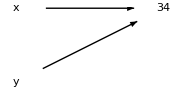

```mathematica
Graphics[{Text[Framed["x"],{0,0}],Arrow[{{0,0},{.5,0}},.1],Text[Framed[34],{.5,0}],
Text[Framed["y"],{0,-.25}],Arrow[{{0,-.25},{.5,0}},.1]},ImageSize->Small]
```

```mathematica
y+4
```

38

```mathematica
x=12
```

12

```mathematica
y+4
```

38

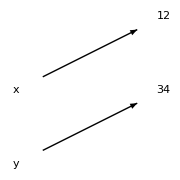

```mathematica
Graphics[{Text[Framed["x"],{0,0}],Arrow[{{0,0},{.5,0.25}},.1],
Text[Framed[12],{.5,0.25}],Text[Framed[34],{.5,0}],
Text[Framed["y"],{0,-.25}],Arrow[{{0,-.25},{.5,0}},.1]},ImageSize->Small]
```

SetDelayed[var,expr] (var:=expr) makes it so that every time that var is called later in the file, then expr called and run to produce a value in the place of var.

```mathematica
x=34
```

34

```mathematica
y:=x
```

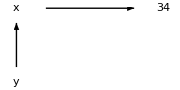

```mathematica
Graphics[{Text[Framed["x"],{0,0}],Arrow[{{0,0},{.5,0}},.1],Text[Framed[34],{.5,0}],
Text[Framed["y"],{0,-.25}],Arrow[{{0,-.25},{0,0}},.05]},ImageSize->Small]
```

```mathematica
y+4
```

38

```mathematica
x=12
```

12

```mathematica
y+4
```

16

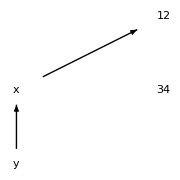

```mathematica
Graphics[{Text[Framed["x"],{0,0}],Arrow[{{0,0},{.5,0.25}},.1],
Text[Framed[12],{.5,0.25}],Text[Framed[34],{.5,0}],
Text[Framed["y"],{0,-.25}],Arrow[{{0,-.25},{0,0}},.05]},ImageSize->Small]
```

#### Function assignment

We can create functions with no arguments

```mathematica
constantSix[]=6
```

6

```mathematica
constantSix[]
```

6

Functions with a dummy argument

```mathematica
constSix[_]=6
```

6

```mathematica
constSix[23]
```

6

If we want to use the parameter in the definition of the function we need to give it a name

```mathematica
identity[z_]=z
```

z

```mathematica
{identity[56],identity[hello],identity[10]}
```

{56,hello,10}

It works, but in Wolfram Language, unless you are not careful the above can result in an issue

```mathematica
y=3
```

3

```mathematica
square[y_]=y^2
```

9

```mathematica
{square[5],square[hello],square[10]}
```

{9,9,9}

The “correct” way would be using the SetDelayed function.

```mathematica
cube[y_]:=y^3
```

```mathematica
{cube[56],cube[hello],cube[10]}
```

{175616,hello^3,1000}

#### Information on values

You can recall the way that you have given assignments to symbols using the Definition function

```mathematica
Definition[y]
Definition[identity]
Definition[square]
Definition[cube]
```

y=3

identity[z_]=z

square[y_]=9

cube[y_]:=y^3

You can ask for more details using the Information function or the ?

```mathematica
?y
?identity
?square
?cube
```

Symbols that have not been referred to at all will throw out Missing object

```mathematica
?bye
```

Missing[UnknownSymbol,bye]

You can also use Information to get information about Built-In symbols

```mathematica
Information[Plot]
```

They look a bit different as they carry templates, options, attributes, and are stored in the System` context.
For example, they all have the Protected attribute which prevents them from being overwritten

```mathematica
Plot=23
```

Set::wrsym: Symbol Plot is Protected.

23

Adding options, attributes and other properties to user defined functions is possible  but we will only see the tip of the iceberg on that in this lecture

#### Names[“Global`*”]

We can check what are the symbols that we as the user have created by using the Names function

```mathematica
Names["Global`*"]
```

{constantSix,constSix,cube,hello,identity,square,x,y,z}

We can use this to build a dashboard with definitions

```mathematica
Grid[{#,If[NumericQ[ToExpression[#]],ToExpression[#],DownValues[Evaluate[ToExpression[#]]]]}&/@Names["Global`*"],Frame->All]
```

constantSix | {HoldPattern[constantSix[]]:>6}
constSix | {HoldPattern[constSix[_]]:>6}
cube | {HoldPattern[cube[y_]]:>y^3}
hello | {}
identity | {HoldPattern[identity[z_]]:>z}
square | {HoldPattern[square[y_]]:>9}
x | 12
y | 3
z | {}

#### Clearing Variables

If we want to clear the values of our user defined symbols there are different methods that will work.

We can use Unset (=.) to remove the assignments done by Set

```mathematica
x
```

12

```mathematica
x=.
```

```mathematica
x
```

x

Or Clear for one or more symbols

```mathematica
Clear[y]
```

```mathematica
y
```

y

```mathematica
Clear[identity, square, cube]
```

```mathematica
identity[z]
```

identity[z]

```mathematica
?identity
```

Their difference

```mathematica
fib[0]=0;
fib[1]=1;
fib[n_]:=fib[n]=fib[n-1]+fib[n-2]
```

```mathematica
fib[3]
```

2

```mathematica
?fib
```

```mathematica
fib[0]=.
```

```mathematica
?fib
```

```mathematica
fib[4]
```

3

```mathematica
Clear[fib]
```

```mathematica
?fib
```

```mathematica
Names["Global`*"]
```

{constantSix,constSix,cube,fib,hello,identity,n,square,x,y,y$,z,z$}

#### ClearAll and Remove

Let us give an attribute to a function

```mathematica
Attributes[f]={Listable}
```

{Listable}

This is similar to “vectorizing” a function in other programing languages

```mathematica
f[{1,2,3}]
```

{f[1],f[2],f[3]}

```mathematica
?f
```

```mathematica
Clear[f]
```

```mathematica
?f
```

```mathematica
ClearAll[f]
```

```mathematica
?f
```

Let us look at one other properties that built-in functions have; syntax coloring

```mathematica
Information[x,y,asd]
```

Information::nonopt: Options expected (instead of asd) beyond position 2 in Information[x,y,asd]. An option must be a rule or a list of rules.

Information[x,y,asd]

We can add this to our user defined functions as follows

```mathematica
SyntaxInformation[f]={"ArgumentsPattern"->{_}}
```

{ArgumentsPattern→{_}}

```mathematica
f[x,y]
```

f[x,y]

```mathematica
ClearAll[f]
```

```mathematica
f[x,y]
```

The above (Unset, Clear, ClearAll) cleared the values, definitions, or even attributes but it still kept the associated symbols in the system memory.

```mathematica
Names["Global`*"]
```

{asd,constantSix,constSix,cube,f,fib,hello,identity,n,square,x,y,y$,z,z$}

We can use Remove, to totally rid ourselves of a user construed symbol

```mathematica
Remove[f]
```

```mathematica
?f
```

Missing[UnknownSymbol,f]

```mathematica
Names["Global`*"]
```

{asd,constantSix,constSix,cube,fib,hello,identity,n,square,x,y,y$,z,z$}

We can even remove the whole set of defined (user) symbols

```mathematica
Remove["Global`*"]
```

```mathematica
Names["Global`*"]
```

{}

### Exercises

Simple Assignments

Clearing/removing

What is the output of:

x=3;
y=x;
x=4;
y^2

x=3;
y:=x;
x=4;
y^2

x=5;
f[x_]=x^2;
f[2]

x=5;
f[x_]:=x^2;
f[2]